```mathematica
Import["/home/jadeleon/Documents/component-erasing-maps/mathematica/quantumJA.m"]
```

```mathematica
badEigVec={};
indices=Subsets[Range[15],{2}];
Do[
eigSys=PCE[Normal[SparseArray[Flatten[{1,indices[[i]]+1}]->ConstantArray[1,3],{16}]]]//Reshuffle//Eigensystem;
negEigPos=Flatten[Position[eigSys[[1]],_?Negative]];
AppendTo[badEigVec,Dirac[eigSys[[2,#]]]&/@negEigPos]
,{i,Length[indices]}]
```

```mathematica
factorized[[105]]
```

{((01+10)_24)⊗11_13,((00+11)_24)⊗10_13,((00+11)_24)⊗01_13,((01+10)_24)⊗00_13}

```mathematica
TwoQBoard[Normal[SparseArray[{{1,1},{1,4},{4,1},{3,4}}->{1,1,1,1},{4,4}]]]
```

-Graphics-

```mathematica
Outer[Times,{1,0,0,1},{1,0,0,1}]
```

{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}}

```mathematica
Dirac[#]&/@(PCE[Normal[SparseArray[{{1,1},{1,4},{4,1},{3,4}}->{1,1,1,1},{4,4}]]//Flatten]//Reshuffle//Eigenvectors)[[3;;4]]
```

{-0110+1100,-0011+1001}

```mathematica
badEigVec[[35]]
```

{0100+1110,-0110+1100,0001+1011,-0011+1001}

```mathematica
PCE[Normal[SparseArray[Flatten[{1,indices[[1]]+1}]->ConstantArray[1,3],{16}]]]//Reshuffle//Eigenvalues
```

{3/4,3/4,3/4,3/4,-1/4,-1/4,-1/4,-1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4}

```mathematica
eigv1=PCE[Normal[SparseArray[Flatten[{1,indices[[1]]+1}]->ConstantArray[1,3],{16}]]]//Reshuffle//Eigenvalues;
Do[
eigv2=PCE[Normal[SparseArray[Flatten[{1,indices[[i]]+1}]->ConstantArray[1,3],{16}]]]//Reshuffle//Eigenvalues;
If[eigv1≠eigv2,
Print["En la iteración "<>ToString[i]<>" encontré eigenvalores no iguales."];
Break
,
eigv1=eigv2;
];
If[i==Length[indices],
Print["Todos los eigenvalores son iguales ALV."]
,
Nothing
]
,
{i,2,Length[indices]}
]
```

Todos los eigenvalores son iguales ALV.

```mathematica
letters={" ","K","e","t","[","]"};
factorized={};
Do[
AppendTo[factorized,{}];
Do[
a=Characters[ToString[badEigVec[[i,j]]]];
indicesEqual={};
indicesEqual1={};
indicesEqual2={};
ketsNum=Length[badEigVec[[i,j]]];
Do[
a=DeleteCases[a,letters[[k]]];
,{k,6}];
If[a[[1]]=="0"∨a[[1]]=="1",PrependTo[a,"+"],Nothing];
a=ArrayReshape[a,{Length[badEigVec[[i,j]]],5}];
If[ketsNum==4,
Do[
AppendTo[indicesEqual1,If[a[[1,k]]==a[[2,k]]=="0"∨a[[1,k]]==a[[2,k]]=="1",k,Nothing]];
AppendTo[indicesEqual2,If[a[[3,k]]==a[[4,k]]=="0"∨a[[3,k]]==a[[4,k]]=="1",k,Nothing]];
,{k,2,5}];indicesDiff1=Delete[Range[5],Join[{{1}},{#}&/@indicesEqual1]];
indicesDiff2=Delete[Range[5],Join[{{1}},{#}&/@indicesEqual2]];
notFact1={};
notFact2={};
Do[
AppendTo[notFact1,If[a[[k,1]]=="+",1,-1]Ket[StringJoin[(a[[k,#]]&/@indicesDiff1)]]];
AppendTo[notFact2,If[a[[k+2,1]]=="+",1,-1]Ket[StringJoin[(a[[k+2,#]]&/@indicesDiff2)]]];
,{k,2}];
indicesFactor1=StringJoin[(ToString[#-1]&/@indicesEqual1)];
indicesDiff1=StringJoin[(ToString[#-1]&/@indicesDiff1)];
factor1=Subscript[Ket[StringJoin[a[[1,#]]&/@indicesEqual1]], indicesFactor1];
parentheses1=Total[notFact1];
indicesFactor2=StringJoin[(ToString[#-1]&/@indicesEqual2)];
indicesDiff2=StringJoin[(ToString[#-1]&/@indicesDiff2)];
factor2=Subscript[Ket[StringJoin[a[[3,#]]&/@indicesEqual2]], indicesFactor2];
parentheses2=Total[notFact2];
AppendTo[factorized[[i]],Subscript[(parentheses1), indicesDiff1]⊗factor1+Subscript[(parentheses2), indicesDiff2]⊗factor2],
If[ketsNum==2,
Do[
AppendTo[indicesEqual,If[AllTrue[a[[All,k]],#=="0"&],k,Nothing]];
AppendTo[indicesEqual,If[AllTrue[a[[All,k]],#=="1"&],k,Nothing]];
,{k,2,5}];
indicesDiff=Delete[Range[5],Join[{{1}},{#}&/@indicesEqual]];
notFact={};
Do[
AppendTo[notFact,If[a[[k,1]]=="+",1,-1] Ket[StringJoin[(a[[k,#]]&/@indicesDiff)]]]
,{k,Length[a]}];
indicesFactor=StringJoin[(ToString[#-1]&/@indicesEqual)];
indicesDiff=StringJoin[(ToString[#-1]&/@indicesDiff)];
factor=Subscript[Ket[StringJoin[a[[1,#]]&/@indicesEqual]], indicesFactor];
parentheses=Total[notFact];
AppendTo[factorized[[i]],Subscript[parentheses, indicesDiff]⊗factor],
Nothing
];
];
,{j,Length[badEigVec[[i]]]}]
,{i,Length[badEigVec]}]
```

## Otra cosa

```mathematica
prueba=PCE[Normal[SparseArray[Flatten[{1,{3,7}+1}]->ConstantArray[1,3],{16}]]]//Reshuffle//Eigensystem
```

{{3/4,3/4,3/4,3/4,-1/4,-1/4,-1/4,-1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4},{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0}}}

```mathematica
(rho=1/2{{1+z,x-I y},{x+I y,1-z}})//MatrixForm
```

((1+z)/2 | 1/2 (x-ⅈ y)
1/2 (x+ⅈ y) | (1-z)/2)

```mathematica
(One={{0,0},{0,1}})//MatrixForm
```

(0 | 0
0 | 1)

```mathematica
KroneckerProduct[rho,One]//MatrixForm
```

(0 | 0 | 0 | 0
0 | (1+z)/2 | 0 | 1/2 (x-ⅈ y)
0 | 0 | 0 | 0
0 | 1/2 (x+ⅈ y) | 0 | (1-z)/2)

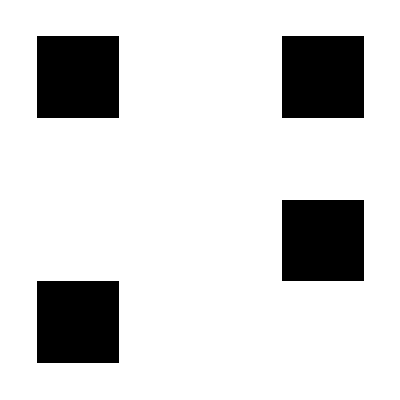

```mathematica
ArrayReshape[{1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0},{4,4}]//ArrayPlot
```

```mathematica
badCh=PCE[{1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0}];rhoTwo=ArrayReshape[badCh.(KroneckerProduct[rho,One]//Flatten),{4,4}]//FullSimplify;
Map[Tr,Partition[rhoTwo,{2,2}],{2}]//FullSimplify//MatrixForm
```

((1+z)/2 | 0
0 | (1-z)/2)

```mathematica
Zero={{1,0},{0,0}};
ArrayReshape[badCh.(KroneckerProduct[rho,Zero]//Flatten),{4,4}]//FullSimplify;
Map[Tr,Partition[%,{2,2}],{2}]//FullSimplify//MatrixForm
```

((1+z)/2 | 0
0 | (1-z)/2)

```mathematica
ArrayReshape[badCh.(KroneckerProduct[rho,IdentityMatrix[2]/2]//Flatten),{4,4}]//FullSimplify;
TensorContract[ArrayReshape[%,{2,2,2,2}],{2,4}]//FullSimplify//MatrixForm
```

((1+z)/2 | 0
0 | (1-z)/2)

```mathematica
Eigensystem[Pauli[3]][[2,1]]
```

{0,1}

```mathematica
q=3;
ArrayReshape[
badCh.Flatten[KroneckerProduct[
Outer[Times,
Normalize[Eigensystem[Pauli[q]][[2,1]]],Normalize[Eigensystem[Pauli[q]][[2,1]]]],rho]]
,
{4,4}];
TensorContract[ArrayReshape[%,{2,2,2,2}],{1,3}]//FullSimplify//MatrixForm
```

((1+z)/2 | 0
0 | (1-z)/2)

```mathematica
TensorContract[ArrayReshape[Outer[Times,{1,0,0,1},{1,0,0,1}],{2,2,2,2}],{2,4}]//FullSimplify
```

{{1,0},{0,1}}

```mathematica
KroneckerProduct[{{1,0},{0,1}},{{1,0},{0,1}}]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Binomial[15,3]
```

455

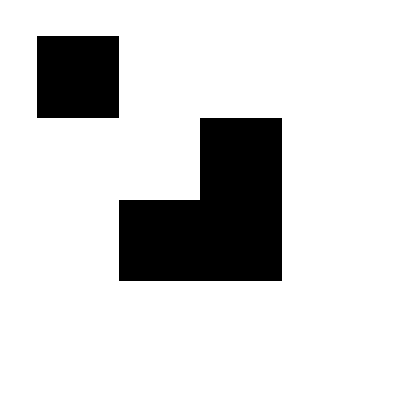

```mathematica
(tablero=Normal[SparseArray[{{1,1},{3,3},{3,2},{2,3}}->ConstantArray[1,4],{4,4}]])//ArrayPlot
badCh=PCE[Flatten[tablero]];
```

```mathematica
q=2;
ArrayReshape[
badCh.Flatten[KroneckerProduct[
Outer[Times,
Normalize[Eigensystem[Pauli[q]][[2,1]]],Normalize[Eigensystem[Pauli[q]][[2,1]]]],rho]]
,
{4,4}];
TensorContract[ArrayReshape[%,{2,2,2,2}],{1,3}]//FullSimplify//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
Norm[{1,0,1,0}]
```

√2

```mathematica
oneQbitValid={};
indices3=Subsets[Range[15],{3}];
Do[
tablero=Normal[SparseArray[Flatten[{1,indices3[[i]]+1}]->ConstantArray[1,4],{16}]];
tablero=ArrayReshape[tablero,{4,4}];
If[√2<Norm[tablero[[1]]]<2∨√2<Norm[Transpose[tablero][[1]]]<2,Continue,
AppendTo[oneQbitValid,tablero]
]
,
{i,Length[indices3]}
]
```

```mathematica
onlyCorr=(If[Norm[#[[1]]]==1&&Norm[Transpose[#][[1]]]==1,#,Nothing])&/@oneQbitValid;
```

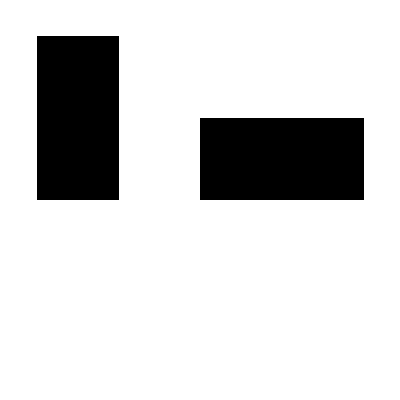

```mathematica
Normal[SparseArray[{{1,1},{2,4},{2,1},{2,3}}->{1,1,1,1},{4,4}]]//ArrayPlot
```

(0 | 0
0 | 1)

((1+z)/2 | 0
0 | (1-z)/2)

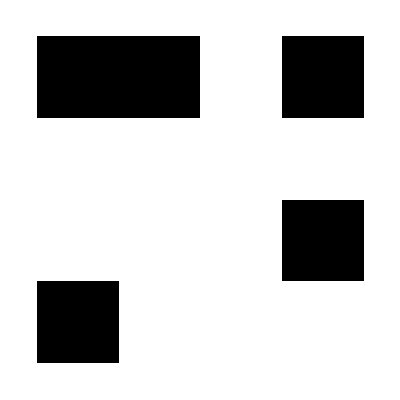

((1+z)/2 | x/2
x/2 | (1-z)/2)

```mathematica
badCh=PCE[Flatten[Normal[SparseArray[{{1,1},{1,4},{4,1},{2,3}}->{1,1,1,1},{4,4}]]]];
q=0;
ith=1;
(rhoP=Outer[Times,
Conjugate[Normalize[Eigenvectors[Pauli[q]][[ith]]]],Normalize[Eigenvectors[Pauli[q]][[ith]]]])//MatrixForm
ArrayReshape[
badCh.Flatten[KroneckerProduct[
rhoP,rho]]
,
{4,4}];
TensorContract[ArrayReshape[%,{2,2,2,2}],{1,3}]//FullSimplify//MatrixForm
```

```mathematica
wtf=((TensorContract[ArrayReshape[
ArrayReshape[
PCE[Flatten[#]].Flatten[KroneckerProduct[
Outer[Times,
Normalize[Eigenvectors[Pauli[0]][[1]]],Normalize[Eigenvectors[Pauli[0]][[1]]]],rho]]
,
{4,4}]
,{2,2,2,2}],{1,3}]//FullSimplify)==DiagonalMatrix[{1/2,1/2}])&/@onlyCorr;
```

```mathematica
AllTrue[wtf,TrueQ]
```

True

#### Conclusión de hoy (15.01.2021)

Para las operaciones PCE de 2 qubits, 4 componentes invariantes que dejan sólo correlaciones invariantes:
cuando el 1 qubit está en el estado de máxima ignorancia 1/2 o en alguno de los eigenestados de σ_xo σ_zel otro qubit se mapea a 1/2. Y cuando el otro qubit está en un eigenestado de σ_y el qubit se manda a cero, osea no es una operación PCE de 1 qubit :O 

Sospecho que no hay condiciones sobre ρ' para que ℰ(ρ⊗ρ') sea una operación PCE de 1 qubit.

```mathematica
tablero=Normal[SparseArray[{{1,1},{3,4},{4,1},{1,2},{1,4},{2,3},{4,3}}->ConstantArray[1,7],{4,4}]];
tablero//TwoQBoard
```

-Graphics-

```mathematica
E1q[list0_,fixed_]:=Module[{list=list0,a,b,c},
$Assumptions=a+c==1;
rhoPrimed={{a,b},{Conjugate[b],c}};
dM={rhoPrimed,rho};
dm=If[fixed==2,Reverse[dM],dM];
TensorContract[ArrayReshape[ArrayReshape[PCE[Flatten[list]].Flatten[KroneckerProduct[dm[[1]],dm[[2]]]],{4,4}],{2,2,2,2}],{fixed,fixed+2}]//FullSimplify
]
```

```mathematica
E1q[tablero,2]//MatrixForm
```

((1+z)/2 | 0
0 | (1-z)/2)

```mathematica
ReducedTwoQBoard[tablero_List,qubit_]:=If[qubit==1,ArrayPlot[SparseArray[Append[#,1]&/@Position[Transpose[tablero][[1]],1]->(If[#[[1]]==1,Black,If[#[[1]]≠1,RGBColor["#CC0000"],Nothing]]&/@Position[Transpose[tablero][[1]],1]),{4,1}]],If[qubit==2,ArrayPlot[SparseArray[Append[#,1]&/@Position[tablero[[1]],1]->(If[#[[1]]==1,Black,If[#[[1]]≠1,RGBColor["#CC0000"],Nothing]]&/@Position[tablero[[1]],1]),{4,1}]]]]
```

```mathematica
ReducedTwoQBoard[tablero,2]
```

-Graphics-

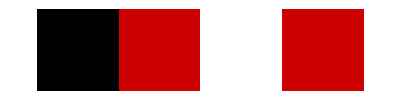

```mathematica
ArrayPlot[{SparseArray[Position[tablero[[1]],1]->(If[#[[1]]==1,Black,If[#[[1]]≠1,RGBColor["#CC0000"],Nothing]]&/@Position[tablero[[1]],1]),{4,1}]}]
```